# Todo:

Technically, my proof of classical universality is incorrect. It doesn’t account for [[0, 0], [0, 0]] or [[1, 1], [1, 1]]
My circuits dont actually work?????

# Exploring Universal Classical and Quantum Gates through Matrix Decomposition

## Theoretical approaches to representing discrete operators as linear state space transformations

## Introduction

### Universal Classical Gates

Classical logic uses logical operators, called gates, that transform one or more boolean-valued inputs to one or more boolean-valued outputs. For example, the AND gate returns True only when both of it’s inputs are True. AND is of the form 2→1, because it takes in two inputs and returns a single output.
An operation of two boolean values can be represented by a truth table, with each axis representing each input.

#### Implementation

```mathematica
(* For Boolean (True or False)-valued functions *)
truthTable[func_, inputName_:"_None"]:=Grid[
  (* Truth Table with Axis Labels *)
 {{If[inputName=="_None", If[StringContainsQ[ToString[func], "&"], "func&", func], inputName], "0", "1"},
  {"0", b2i@func[False, False], b2i@func[False, True]},
  {"1", b2i@func[True, False], b2i@func[True, True]}},
  
 (* Dividers to seperate inputs and outputs *)
 Dividers->{{2->True}, {2->True}},
 
 (* Alligns the input labels to the right *)
 Alignment->{Right, Baseline},
 
 (* Color based on the value of each cell *)
 Background->{None, None, Flatten@Table[
  {b1, b2}->If[
     func[i2b[b1-2], i2b[b2-2]],
     SetAlphaChannel[Green, 0.5],
     SetAlphaChannel[Red, 0.5]],
    {b2, {2, 3}},
    {b1, {2, 3}}]}]

(* For Integer Boolean (1 or 0)-valued functions *)
numericalTruthTable[func_, inputName_:"_None"]:=Grid[
  (* Truth Table with Axis Labels *)
 {{If[inputName=="_None", If[StringContainsQ[ToString[func],"&"], "func&", func], inputName], "0", "1"},
  {"0", func[0, 0], func[0, 1]},
  {"1", func[1, 0], func[1, 1]}},
  
 (* Dividers to seperate inputs and outputs *)
 Dividers->{{2->True}, {2->True}},
 
 (* Alligns the input labels to the right *)
 Alignment->{Right, Baseline},
 
 (* Color based on the value of each cell *)
 Background->{None, None, Flatten@Table[
  {b1, b2}->
   (func[b1-2, b2-2])SetAlphaChannel[Green, 0.5]+(1-func[b1-2, b2-2])SetAlphaChannel[Red, 0.5],
    {b2, {2, 3}},
    {b1, {2, 3}}]}]
```

#### Example

```mathematica
truthTable[And]
```

And | 0 | 1
0 | 0 | 0
1 | 0 | 1

Some gates are able to be composed with themselves to make any other possible gate. These gates are called universal gate.
There are only two universal, classical, 2→1 gates: NAND (⊼) and NOR (⊽). For example, here is how the NAND gate can represent the XOR gate with a circuit diagram and code:
-Graphics-

```mathematica
(* Built-In XOR *)
xor1[a_, b_]:= Xor[a, b];

(* XOR from NAND gates *)
xor2[a_, b_]:=(((a⊼a)⊼(b⊼b))⊼(a⊼b))⊼(((a⊼a)⊼(b⊼b))⊼(a⊼b));

(* Display Truth Tables *)
Row[{truthTable[xor1], Spacer[10], truthTable[xor2]}]
```

xor1 | 0 | 1
0 | 0 | 1
1 | 1 | 0xor2 | 0 | 1
0 | 0 | 1
1 | 1 | 0

Here is every gate represented with the built-in function, with only NANDs, and with only NORs:

#### Universal Function Definitions

```mathematica
and1[a_, b_]:=And[a, b];
and2[a_, b_]:=(a⊼b)⊼(a⊼b);
and3[a_, b_]:=(a⊽a)⊽(b⊽b);

or1[a_, b_]:=Or[a, b];
or2[a_, b_]:=(a⊼a)⊼(b⊼b);
or3[a_, b_]:=(a⊽b)⊽(a⊽b);

xor1[a_, b_]:=Xor[a, b];
xor2[a_, b_]:=(((a⊼a)⊼(b⊼b))⊼(a⊼b))⊼(((a⊼a)⊼(b⊼b))⊼(a⊼b));
xor3[a_, b_]:=(((a⊽b)⊽(a⊽b))⊽((a⊽b)⊽(a⊽b)))⊽((a⊽a)⊽(b⊽b));

nand1[a_, b_]:=Nand[a, b];
nand2[a_, b_]:=a⊼b;
nand3[a_, b_]:=((a⊽a)⊽(b⊽b))⊽((a⊽a)⊽(b⊽b));

nor1[a_, b_]:=Nor[a, b];
nor2[a_, b_]:=((a⊼a)⊼(b⊼b))⊼((a⊼a)⊼(b⊼b));
nor3[a_, b_]:=a⊽b;

xnor1[a_, b_]:=Xnor[a, b];
xnor2[a_, b_]:=(((a⊼a)⊼(b⊼b))⊼(a⊼b));
xnor3[a_, b_]:=((((a⊽b)⊽(a⊽b))⊽((a⊽b)⊽(a⊽b)))⊽((a⊽a)⊽(b⊽b)))⊽((((a⊽b)⊽(a⊽b))⊽((a⊽b)⊽(a⊽b)))⊽((a⊽a)⊽(b⊽b)))
```

#### Universal NAND Visualization

```mathematica
Grid[
Transpose@(truthTable[#]&/@#&/@{{and1, and2, and3}, {or1, or2, or3}, {xor1, xor2, xor3}, {nand1, nand2, nand3}, {nor1, nor2, nor3}, {xnor1, xnor2, xnor3}}),
Spacings->{3, 2}]
```

and1 | 0 | 1
0 | 0 | 0
1 | 0 | 1 | or1 | 0 | 1
0 | 0 | 1
1 | 1 | 1 | xor1 | 0 | 1
0 | 0 | 1
1 | 1 | 0 | nand1 | 0 | 1
0 | 1 | 1
1 | 1 | 0 | nor1 | 0 | 1
0 | 1 | 0
1 | 0 | 0 | xnor1 | 0 | 1
0 | 1 | 0
1 | 0 | 1
and2 | 0 | 1
0 | 0 | 0
1 | 0 | 1 | or2 | 0 | 1
0 | 0 | 1
1 | 1 | 1 | xor2 | 0 | 1
0 | 0 | 1
1 | 1 | 0 | nand2 | 0 | 1
0 | 1 | 1
1 | 1 | 0 | nor2 | 0 | 1
0 | 1 | 0
1 | 0 | 0 | xnor2 | 0 | 1
0 | 1 | 0
1 | 0 | 1
and3 | 0 | 1
0 | 0 | 0
1 | 0 | 1 | or3 | 0 | 1
0 | 0 | 1
1 | 1 | 1 | xor3 | 0 | 1
0 | 0 | 1
1 | 1 | 0 | nand3 | 0 | 1
0 | 1 | 1
1 | 1 | 0 | nor3 | 0 | 1
0 | 1 | 0
1 | 0 | 0 | xnor3 | 0 | 1
0 | 1 | 0
1 | 0 | 1

### State Vector Representation of Operations

Classical 2→1 gates are usually considered to be a function with two inputs and one output. However, there is an alternative interpretation of gates as a linear operation on a unit basis vector representing the systems total state. This allows for all operations to be represented as matrix multiplications, and generalizes easily to quantum circuits.

#### State Vector

Let   𝔹   be   the   set   of   binary   numbers   {0, 1} .

An n-bit system can be represented with a vector in 𝔹^n, such that each dimension of the vector corresponds to a bit in the state. A gate can be considered to be an association of each input state—of the  total  possible states—to a specific output state.
A vector can be constructed in 𝔹^(2^n) so that each dimension corresponds to a possible state. Thus, a unit basis vector of 𝔹^(2^n) represents one singular state. A matrix transforms the ith basis vector e_i to the ith column in the matrix V_i.

For example, in the 4-bit binary system 1011, there are  possible states, so the 16-dimensional state vector representing this system is [0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0].
Note that the state vector of the binary number n (11 in this example) is the basis vector e_n, assuming the vector is indexed from 0.

#### Gate Application to a State Vector

A matrix M = [V_0 | V_1 | V_2 | V_3 | V_4 | V_5 | V_6 | V_7 | V_8 | V_9 | V_10 | V_11 | V_12 | V_13 | V_14 | V_15], where V_i∈𝔹^(2^n), takes the ith basis vector to V_i (i.e., M\[Application]e_i=V_i).
This means that M can associate each basis vector e_i to a specific output vector V_i, so, by our definition of a gate operation, this matrix can apply any arbitrary gate.

#### Motivation

The reason for representing gates as matrix multiplication is two-fold:
Firstly, in this representation, all gates are linear transformations, which can be easily composed and reasoned about. A whole circuit, made up of many gate operations, can be simplified to just a single matrix. Thus, the problem of determining whether a set of gates is universal is equivalent to the problem of whether every gate matrix can be decomposed into a product of elements in that set.
Secondly, quantum systems exhibit phenomena such as superposition and entanglement, in which a quantum state may be in a linear combination of multiple states at the same time, and in which a full state can not be represented as the tensor product of individual qubit states, respectively. This means that an n-bit quantum state can be represented by a vector on the complex unit hypersphere of ℂ^(2^n). The reason it must be on the unit hypersphere is because the magnitude of the vector must be equal to one, which is equivalent to the statement that the sum of the probabilities of the states of a random system is one.

### Universal Quantum Gate Sets

TODO

## Implementation

### Boolean State Vectors

#### Booleans

Here are a variety of helper functions which convert between bools (b), integers (i), and state vectors (v):

```mathematica
b2i[b_]:=If[b, 1, 0];
b2i[b_List]:=b2i/@b
i2b[b_]:=b==1;
i2b[b_List]:=i2b/@b

b2v[b_]:=If[b, {0, 1}, {1, 0}]
i2v[b_Integer]:=If[b==1, {0, 1}, {1, 0}]
v2i[{v1_Integer, v2_Integer}]:=v1*1+v2*0
```

#### Tensors and State Construction

A state containing multiple bits is constructed by taking the tensor product of each consecutive bit’s state. tensor takes the tensor product of vectors, and fullState constructs the state vector of a list of boolean values.

```mathematica
tensor[v__] := Flatten[TensorProduct[v]]
fullState[b_List]:=tensor@@i2v/@b
```

### Matrix Definitions

Each matrix representing an operation has a different form. For example, the NOT matrix is {{0, 1}, {1, 0}}.
Some matrices are constant and worked out by hand beforehand.
Other matrix operations may need arguments, and so has to be computed. This is done by computing the desired output for each input, then representing the inputs and outputs as state vectors, then constructing the M matrix from each output V_i.

#### Constant Matrices

```mathematica
I2 = ({{1, 0}, {0, 1}}); (* Identity Matrix *)
matrixNot = ({{0, 1}, {1, 0}});

matrixCopy = ({{1, 1, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 1, 1}});
matrixNand = ({{0, 0, 0, 0}, {1, 1, 0, 0}, {0, 0, 0, 1}, {0, 0, 1, 0}});
```

Here is a visualization of each of those matrices:

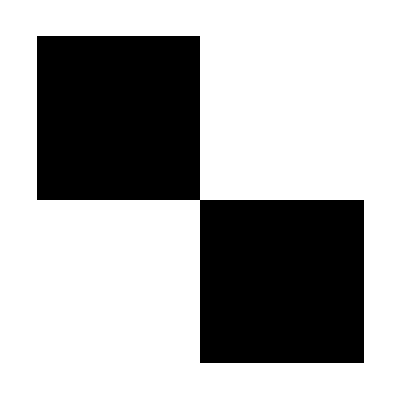
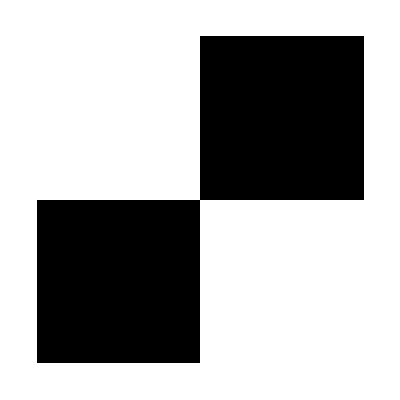
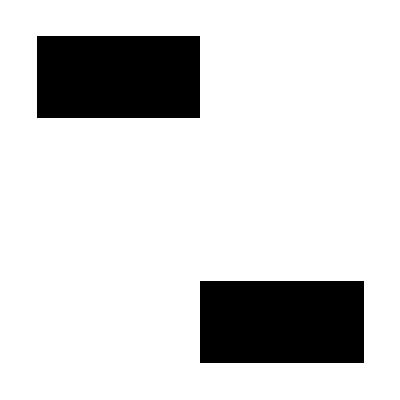
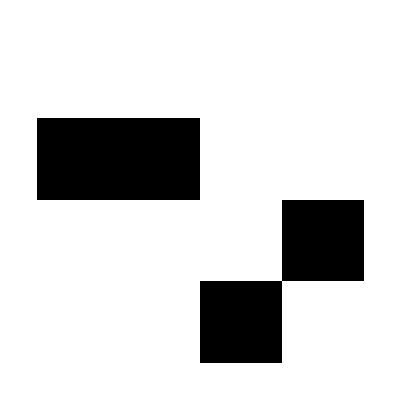
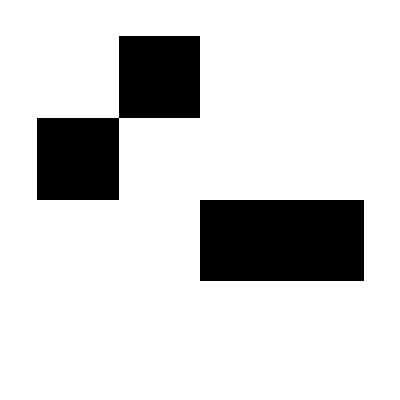

```mathematica
ArrayPlot/@{I2, matrixNot, matrixCopy, matrixNand, matrixNor}
```

#### Computed Matrices

Swap switches two bits at positions s1 and s2.

```mathematica
Vi1[i_, n_, s1_, s2_]:=Module[{bv, sbv},
bv=IntegerDigits[i, 2, n];
sbv=fullState[Table[bv[[Switch[j, s1, s2, s2, s1, _, j]]], {j,n}]]]
matrixSwap[n_, s1_, s2_]:=Table[Vi1[i, n, s1, s2], {i, 0, 2^n-1}]
```

Return reduces the number of bits, thereby creating a smaller subset of the original bits to use as an output.

```mathematica
Vi2[i_, n_, s1_, s2_]:=tensor@@i2v/@(IntegerDigits[i, 2, n])[[Span[s1, s2]]]
matrixReturn[n_, s1_, s2_]:=Transpose[Vi2[#, n, s1, s2]&/@Range[0, 2^n-1]]
```

For example, here is how a state vector of length 2^5=32 is reduced to a single bit state vector:

```mathematica
matrixReturn[5, 1, 1]//MatrixForm
```

(1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1)

Expand increases the number of bits, initializing the circuit to a particular state, either of the form
matrixZeroExpand[a, b] → │ab0000...⟩
or
matrixRepeatExpand[a, b] → │ababab...⟩.

```mathematica
matrixZeroExpand[n_, s1_, s2_]:=Module[{ω1, ω2, Ω1, Ω2},
 ω1=s1-1; Ω1=2^ω1; (* ω1 is the number of bits of the input, Ω1 is the size of the state vector of the input. *)
 ω2=s2; Ω2=2^ω2;   (* ω2 is the number of bits of the output, Ω2 is the size of the state vector of the output. *)
 Table[Module[{Vω1, Vω2, VΩ2},
  Vω1=IntegerDigits[i, 2, ω1];
  Vω2=Join[Vω1, ConstantArray[0, ω2-ω1]];
  VΩ2=fullState[Vω2];
  VΩ2], {i, 0, Ω1-1}]]//Transpose

matrixRepeatExpand[n_, s1_, s2_]:=Module[{ω1, ω2, Ω1, Ω2},
 ω1=s1-1; Ω1=2^ω1; (* ω1 is the number of bits of the input, Ω1 is the size of the state vector of the input. *)
 ω2=s2; Ω2=2^ω2;   (* ω2 is the number of bits of the output, Ω2 is the size of the state vector of the output. *)
 Table[Module[{Vω1, Vω2, VΩ2},
  Vω1=IntegerDigits[i, 2, ω1];
  Vω2=Flatten[ConstantArray[Vω1, ⌈ω2/ω1⌉]][[;;ω2]];
  VΩ2=fullState[Vω2];
  VΩ2], {i, 0, Ω1-1}]]//Transpose
```

For example, here are the expansion matrices increasing a systems wire count from 2 to 5

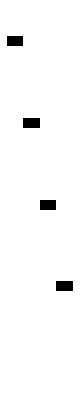
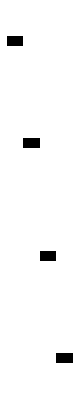

```mathematica
ArrayPlot/@{matrixZeroExpand[5, 3, 5], matrixRepeatExpand[5, 3, 5]}
```

### Gates to Matrices

In order to apply a 2-bit gate to a >2-bit system, the matrix cannot be multiplied directly with the state vector of the entire system. Rather, the gate matrix needs to be composed with Identity matrices representing the lack of operations on other bits. The computed matrices, because they are in a shape other than 2^2 x2^2, are made in the correct dimension, so they are able to apply to the whole state. Here is how each gate is converted to a matrix:

```mathematica
matrixFormOfColumn[G_, n_] :=
  (* M = G[[2]] *)
  (* s1 = G[[1, 1]] *)
  (* s2 = G[[1, 2]] *)
  If[MatchQ[G[[2]], _List], (* For fixed matrices *)
   
    KroneckerProduct[IdentityMatrix[2^(G[[1,1]]-1), TargetStructure->"Sparse"], SparseArray@G[[2]], IdentityMatrix[2^(n - G[[1, 2]]), TargetStructure->"Sparse"]],
    
   SparseArray@G[[2]][n, G[[1, 1]], G[[1, 2]]]] (* Computed matrix: uses Mtype[n, s1, s2] *)
```

For example, here is how the NAND gate is represented when applied to the last two bits of a 4-bit system. The repeating NAND pattern can be seen on the least significant bits, and the diagonal identity pattern can be seen on the more significant bits.

```mathematica
matrixFormOfColumn[{{1, 2}, matrixNand}, 4]//ArrayPlot
```

-Graphics-

### Circuits Implementation

#### Circuit Application

A circuit is the composition of a set of gates applied to a set of wires. Because each gate is represented by a matrix, application of a gate is equivalent to multiplication of a state vector by a matrix. Because matrix multiplication is associative, all of the matrices of a circuit can be multiplied together into a single total circuit matrix. As most circuits require many more internal wires than input or output wires, a circuit matrix can be precomputed (which will take a relatively large amount of time) and then applied to one or more input state vectors (which will take a relatively small amount of time).
Finally, we can convert apply circuit to a logical function which can be displayed.
Here is the code that does this, first computing each matrix for each gate, then composing them by multiplication, then applying them to an input state, then creating a logic function from that:

```mathematica
circuitMatrices[circuit_]:= With[{n = Max@Flatten@circuit[[All, 1]]}, matrixFormOfColumn[#, n]& /@ circuit];
circuitMatrix[circuit_]:= Dot @@ Reverse @ circuitMatrices[circuit]
applyCircuit[circuit_, state_]:= circuitMatrix[circuit].state
logicFunctionFromCircuit[circuit_]:=(applyCircuit[circuit, fullState[{#1, #2}]] // v2i)&  (* Only works for 2->n logic gates *)
```

#### Circuit Visualization

Using the Wolfram Quantum Framework Paclet, my circuits can be converted into the paclet’s representation of a circuit, which can then be displayed. The paclet is also much more optimized, so I may use it’s code to more quickly compute matrix applications

```mathematica
PacletInstall["Wolfram/QuantumFramework"];

quantumOperatorFormOfColumn[i_Integer, gates_, n_]:=
Module[{G, s1, s2, M},
 G=gates[[i]];
 s1=G[[1, 1]];
 s2=G[[1,2]];
 M=G[[2]];

(* Switch for irregular functions *)
 Switch[M,
  matrixSwap,{{-Graphics-, QuantumOperator}}["SWAP",{s1, s2}],
  matrixReturn,{{-Graphics-, QuantumMeasurementOperator}}["Z", If[s1==s2, {s1}, {s1, s2}]],
  matrixCNOT, {{-Graphics-, QuantumOperator}}["CNOT",{s1, s2}],
  matrixZeroExpand, {{-Graphics-, QuantumOperator}}[matrixZeroExpand[n, s1, s2], {s1, s2}],
  matrixRepeatExpand, {{-Graphics-, QuantumOperator}}[matrixRepeatExpand[n, s1, s2], {s1, s2}],
  _,{{-Graphics-, QuantumOperator}}[M, {s1, s2}]
  ]
 ]
 
quantumCircuit[gates_]:=Module[{n=Max@@Flatten@gates[[All,1]],quantumGates, firstIndices},
  quantumGates=quantumOperatorFormOfColumn[#, gates, n]&/@Range[Length[gates]];
  firstIndices=gates[[All, 1, 1]];
  {{-Graphics-, QuantumCircuitOperator}}[Table[quantumGates[[i]]->firstIndices[[i]], {i, Range[Length[gates]]}]]
]


circuitPlot[gates_, imSize_:Medium]:=Module[{quantumGates, firstIndices, qc},
  Image[quantumCircuit[gates]["Diagram"], ImageSize->imSize]
]
```

### Example XOR Circuits

Now that we can create, apply, and visualize a circuit to an input, here are some circuits that perform the XOR gate using only the NAND gate:

```mathematica
XorFromNandGatesCircuit = {
(* Makes use of SWAP, NAND, and COPY *)
   {{3, 5}, matrixZeroExpand},
   {{2, 3}, matrixCopy},
   {{2, 3}, matrixNand},
   {{1, 2}, matrixSwap},
   {{3, 4}, matrixSwap},
   {{2, 3}, matrixCopy},
   {{2, 3}, matrixNand},
   {{1, 2}, matrixNand},
   {{3, 4}, matrixNand},
   {{2, 3}, matrixSwap},
   {{3, 4}, matrixNand},
   {{4, 5}, matrixCopy},
   {{4, 5}, matrixNand},
   {{5, 5}, matrixReturn}
   };

XorFromNandGatesCircuitNoCopy = {
(* Longer, but only makes use of SWAP and NAND *)
{{3, 12}, matrixRepeatExpand},
{{4, 5}, matrixSwap},
{{10, 11}, matrixSwap},
{{1, 2}, matrixNand},
{{3, 4}, matrixNand},
{{5, 6}, matrixNand},
{{7, 8}, matrixNand},
{{9, 10}, matrixNand},
{{11, 12}, matrixNand},
{{4, 5}, matrixSwap},
{{10, 11}, matrixSwap},
{{5, 6}, matrixNand},
{{11, 12}, matrixNand},
{{2, 5}, matrixSwap},
{{8, 11}, matrixSwap},
{{5, 6}, matrixNand},
{{11, 12}, matrixNand},
{{6, 11}, matrixSwap},
{{11, 12}, matrixNand},
{{12, 12}, matrixReturn}
   };
```

As you can see, if we run these two circuits, we get the same truth table as XOR:

```mathematica
numericalTruthTable[logicFunctionFromCircuit[XorFromNandGatesCircuit], "XorWithCopy"]

(* Takes a really long time to run, because large circuits are extremely inefficient. Like it literally took 1047 seconds to run a single XOR gate. Do not run this. Seriously. *)
numericalTruthTable[logicFunctionFromCircuit[XorFromNandGatesCircuitNoCopy], "XorWithoutCopy"]
```

XorWithCopy | 0 | 1
0 | 1 | 0
1 | 0 | 1

$Aborted

We can visualize these quantum circuits using the quantum circuit diagram from the Wolfram Quantum Framework paclet:

```mathematica
Column[{Labeled[circuitPlot[XorFromNandGatesCircuit], "XOR With Copy"], Labeled[circuitPlot[XorFromNandGatesCircuitNoCopy], "XOR Without Copy"]}, Spacings->5]
```

-Graphics-XOR With Copy
-Graphics-XOR Without Copy

For the smaller XOR circuit which uses copy, we can easily visualize the matrices that make up the circuit:
The first and last matrices are not square, because they setup and measure the state vector, respectively.
The interior gate matrices are usually mostly on the diagonal, because they are composed of many identity matrices but only one gate matric.

```mathematica
ArrayPlot /@ circuitMatrices[XorFromNandGatesCircuit]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Here is the composition of all of the interior matrices:

```mathematica
ArrayPlot @circuitMatrix[XorFromNandGatesCircuit[[2;;-2]]]
```

-Graphics-

And here is the final composition of all the matrices, which makes a matrix representation of XOR:

```mathematica
ArrayPlot @circuitMatrix[XorFromNandGatesCircuit]
```

-Graphics-

## Universal Gates Definitions

### Definition

A set of universal gates is a decomposition problem
TODO

#### Classical Definition

A set of gates is universal if, for all possible 2x2 gates T, there exists an equivalent circuit with some number of wires w and some number of gates m such that the columns c_i of the circuit apply a gate to wires λ_1 through λ_2. Formally,
S_g is a set of universal gates iff ∀G∈S_G,∀G_I∈G,G_i∈{e_1, e_2, e_3, e_4} of 𝔹^4,∀{T∈𝔹^(4×4)|∀T_i∈T,T_i∈{e_1, e_2, e_3, e_4} of 𝔹^4}∃w∈ℕ, m∈ℕ|(P∈𝔹^(2^w×4)|∀P_i∈P,P_i∈{e_1, e_2, e_3, e_4}of 𝔹^4 )×((c_1×c_2... c_m)|c_i∈{I_2^(⊗λ_1)⊗G⊗I_2^(⊗λ_2)∀λ_1∈ℕ, λ_2∈ℕ|G∈S_G∧λ_1+2+λ_2==w}))×(R∈𝔹^(4×2^w)|∀R_i∈R,R_i∈{e_1, e_2, e_3, e_4} of 𝔹^4)==T,
where P and R are state preparation and reduction matrices, respectively.

#### Quantum Definition

Very similar to the classical definition, but with a few requirements for quantum gates and the possibility of complex unit vectors. Thus,
S_g is a set of quantum universal gates iff ∀G∈S_G,G is unitary∧∀G_i∈G,||G_i||==1},∀{T∈ℂ^(4×4)|T is unitary∧∀T_i∈T,||T_i||==1}∃w∈ℕ, m∈ℕ|(P∈𝔹^(2^w×4)|∀P_i∈P,P_i∈{e_1, e_2, e_3, e_4} of 𝔹^4)×((c_1×c_2... c_m)|c_i∈{I_2^(⊗λ_1)⊗G⊗I_2^(⊗λ_2)∀λ_1∈ℕ, λ_2∈ℕ|G∈S_G∧λ_1+2+λ_2==w}))×(R∈𝔹^(4×2^w)|∀R_i∈R,R_i∈{e_1, e_2, e_3, e_4}of 𝔹^4 )==T,
where P and R are state preparation and reduction matrices, respectively.

## Classical Universality

### Classical 2→1 Universality Proof

#### Theorem

A gate set containing at least one gate that satisfies each of the following properties is universal:

G(a, a) = ¬a

G(0, 0) + G(0, 1) + G(1, 0) + G(1, 1) is Odd

#### Lemma 1:

In order to make a 2→1 NOT gate, a gate set must have a gate which satisfies the property G(a, a) = ¬a.

In order for a gate to be universal, it needs to be able to implement any 2-bit gate, including the 2-bit NOT gates: (0 | 1 | 0 | 1
1 | 0 | 1 | 0) or (0 | 0 | 1 | 1
1 | 1 | 0 | 0). The 2-bit NOT gates comprise a 1-bit NOT gate on a single wire, and a 1-bit NOT gate can be constructed by using only that single bit of the 2-bit version. Thus, the ability of a gate set to construct a 2-bit NOT gate is equivalent to it’s ability to construct a 1-bit NOT gate.
The only way for a 1-bit NOT gate to be constructed from a 2→1 gate is if the gate satisfies the property that G(a, a) = ¬a, because the input wire to the gate can be duplicated, thus constructing a NOT gate.

#### Lemma 2:

The parity of a 2→1 gate remains unchanged under NOT transformations.

Define the parity of a gate to be the parity of the sum of the digits in it’s truth table. I.e., whether or not the gate has an odd or even number of 1-valued outputs.
The truth table of a gate constructed from applying a NOT gate to it’s first wire then applying some other 2→1 gate is equivalent to the truth table of the other gate mirrored horizontally. The same is true for NOT gates applied to the second input being equivalent to a vertical mirroring of the original truth table. Moving the values of a truth table does not change the parity, so these transformations of a gate preserve parity.
The truth table of a gate constructed by applying a not gate to the output of some other gate also preserves parity, because all the outputs of 0 will turn to 1, and there are 4-n 0s in the truth table for a gate with n 1s, and subtraction from an even number preserves parity.

#### Corollary to Lemma 2:

2→1 gates with even parity can be decomposed into 1-bit NOT gates.

The identity truth table represents a gate which has no effect on the wires of the circuit. Because the identity gate has even parity, this means that it is equivalent to all other gates of even parity under NOT gate transformations.
As identity gates can be removed with no effect to the circuit, any even parity gate is equivalent to some transformation of 1-bit not gates. If a gate set already has the ability to implement NOT gates, which every universal set must by Lemma 1, then gates with even parity are always decomposable into other gates of the set.

#### Proof:

By Lemma 1, all universal gate sets must have a gate with the property G(a, a) = ¬a.
By the Corollary to Lemma 2, gates with even parity are decomposable to NOT, so a universal gate set must contain a gate with odd parity.

#### Results:

Out of all of the possible 2→1 gates

```mathematica
truthTable[BooleanFunction[#, 2], "func"<>ToString[#]]&/@Range[0, 15]
```

{func0 | 0 | 1
0 | 0 | 0
1 | 0 | 0,func1 | 0 | 1
0 | 1 | 0
1 | 0 | 0,func2 | 0 | 1
0 | 0 | 1
1 | 0 | 0,func3 | 0 | 1
0 | 1 | 1
1 | 0 | 0,func4 | 0 | 1
0 | 0 | 0
1 | 1 | 0,func5 | 0 | 1
0 | 1 | 0
1 | 1 | 0,func6 | 0 | 1
0 | 0 | 1
1 | 1 | 0,func7 | 0 | 1
0 | 1 | 1
1 | 1 | 0,func8 | 0 | 1
0 | 0 | 0
1 | 0 | 1,func9 | 0 | 1
0 | 1 | 0
1 | 0 | 1,func10 | 0 | 1
0 | 0 | 1
1 | 0 | 1,func11 | 0 | 1
0 | 1 | 1
1 | 0 | 1,func12 | 0 | 1
0 | 0 | 0
1 | 1 | 1,func13 | 0 | 1
0 | 1 | 0
1 | 1 | 1,func14 | 0 | 1
0 | 0 | 1
1 | 1 | 1,func15 | 0 | 1
0 | 1 | 1
1 | 1 | 1}

there exist only two gates which individually satisfy both of the properties given above:

```mathematica
truthTable[BooleanFunction[#, 2], "func"<>ToString[#]]&/@{7, 14}
```

{func7 | 0 | 1
0 | 1 | 1
1 | 1 | 0,func14 | 0 | 1
0 | 0 | 1
1 | 1 | 1}

Thus, these two gates, the NAND and NOR, respectively, are the only two gates which are individually universal.

### Classical 2→2 Universality Proof

#### Theorem:

Any 2→1 universal gate set can be made into a 2→2 universal gate set.

#### Lemma 1:

All 2→2 gates can be decomposed into two 2→1 gates (G_α(x, y), G_β(x, y)).

#### Lemma 2:

Any of the following forms allow a 2→1 gate to be constructed by only using a single output bit of a 2→2 gate:
(G(x, y), 0), (G(x, y), 1), (0,G(x, y)), (1, G(x, y)),
(G(x, y), x), (G(x, y), y), (x,G(x, y)), (y,G(x, y))

#### Proof:

Thus, the gates of any 2→1 universal gate set can be transformed into 2→2 gates which themselves are universal to the 2→2 gates.
(Although there are also more ways to construct universal 2→2 gates.

## Quantum Universality

### Single Qubit Gates

#### Bloch Sphere Implementation

```mathematica
(* BlochSphere[s_] := {2*Re[s[[1]]*s[[2]]], 2*Im[s[[1]]*s[[2]]], Abs[s[[1]]]^2 - Abs[s[[2]]]^2} *)

BlochSphere[state_] := Module[{θ, φ},
  (* Calculate angles θ and φ from the state vector *)
  θ = 2 ArcCos[Abs[state[[1]]]];
  φ = Arg[state[[2]]];
  {Sin[θ] Cos[φ], Sin[θ] Sin[φ], Cos[θ]}
]

qubitStateGraphics[s_, imSize_:Large]:=
 Graphics3D[{
   (* Draw Transparent Bloch Sphere *)
   Opacity[0.4],
   Sphere[{0, 0, 0},1],
   Opacity[1],
   
   (* Axes and Labels *)
   Black,
   Arrow[{{0, 0, 0},{1.3, 0, 0}}], Text["X Axis", {1.5, 0, 0}],
   Arrow[{{0, 0, 0},{0, 1.3, 0}}], Text["Y Axis", {0, 1.5, 0}],
   Arrow[{{0, 0, 0},{0, 0, 1.3}}], Text["Z Axis", {0, 0, 1.5}],
   
   (* Display State Vector *)
   Red,
   Arrow[{{0, 0, 0},1.3*BlochSphere[s]}], Text[ToString[N[s]], 1.5*BlochSphere[s]]
  },
  
  (* Options *)
  ViewVector->{10, 7, 5},
  Boxed->False,
  ImageSize->imSize,
  PlotRange->1.5{{-1, 1}, {-1, 1}, {-1, 1}}
 ]

singleQubitGatesGraphics[g_, imSize_:Large]:=
 Manipulate[Module[{state, M},
  (* Generate State from Gates *)
  M=Dot@@Reverse@g[[1;;i]];
  state=M.{1, 0};
  qubitStateGraphics[state, imSize]
 ],
 {i, 0, Length[m], 1}
]
```

#### Bloch Sphere Visualization

A Bloch Sphere is a visualization of a qubit state α|0⟩+β|1⟩, where α, β ∈ ℂ^2 such that (|α|)^2+(|β|)^2=1. Although a space of two complex numbers is isomorphic to ℝ^4, not ℝ^3, the global phase of a state has no physical significance, and can be discarded, leaving only three dimensions necessary to be visualized.
For example, here is a Bloch sphere visualizing the arbitrary Y rotation gate:

```mathematica
θ=Pi/3;
qubitStateGraphics[{1,0}.RotationMatrix[-0.5θ], Large]
```

-Graphics3D-

#### Quantum Matrix Definitions

```mathematica
gateRX[θ_] := ({{Cos[θ/2], -ⅈ Sin[θ/2]}, {-ⅈ Sin[θ/2], Cos[θ/2]}})//N;
gateRY[θ_] := ({{Cos[θ/2], -Sin[θ/2]}, {Sin[θ/2], Cos[θ/2]}})//N;
gateRZ[θ_] := ({{1, 0}, {0, Cos[θ]+ⅈ Sin[θ]}})//N;
gateX = ({{0, 1}, {1, 0}})//N;  (* Equivalent to gateRX[π] *)
gateT = ({{1, 0}, {0, 1/(√2)+ⅈ/(√2)}})//N;  (* Equivalent to gateRZ[π/2] *)
gateK = gateRY[Pi/2];

gateH = 1/(√2)({{1, 1}, {1, -1}})//N;
gateS = ({{1, 0}, {0, ⅈ}})//N;
gateCNOT = ({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 0, 1}, {0, 0, 1, 0}});
```

#### Fact 1:

An arbitrary rotation in any axis can be done with only a single arbitrary rotation and a 90 degree rotation

#### Fact 2:

H = Y^(1/2)R_z(π)Y^(1/2)Y^(1/2)

#### Fact 3:

For an R_z(θ)=(R_z(φ))^(⌊θ/φ⌉), ε≤φ/2, where ε = max(‖R_z(θ)-(R_z(φ))^(⌊θ/φ⌉)‖) for a norm of the sum of the lengths of the columns. For most ε, φ « θ.